```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["128_cv.dat","Table"];
MagnetData = Import["128_magnetization.dat","Table"];
SusceptData = Import["128_susceptibility.dat","Table"];
```

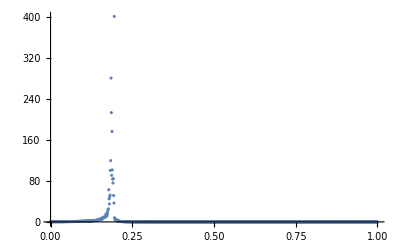

```mathematica
ListPlot[Take[SusceptData], PlotRange->Full]
```

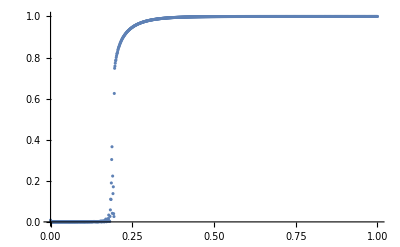

```mathematica
ListPlot[Abs[MagnetData]]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{100,220}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{A,Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{134.574 ⅇ^(-25853. (-0.187882+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 134.574 | 7.6755 | 17.533 | 1.19094×10^-34
Sigma | 0.00439774 | 0.000289629 | 15.184 | 1.58518×10^-29
mu | 0.187882 | 0.000289629 | 648.699 | 1.8962×10^-211}

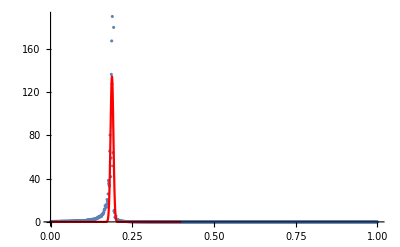

```mathematica
Show[ListPlot[SusceptData,PlotRange->Full],Plot[SusceptFit[x],{x,0,0.4},PlotRange->{{0,0.4},{0,500}}, PlotStyle->Red]]
```

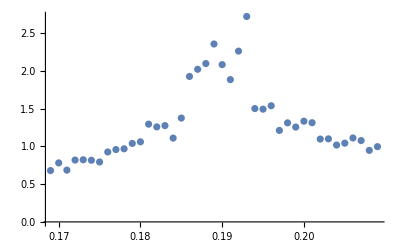

```mathematica
ListPlot[Take[CvData,{170,210}]]
```